```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<TheDiractionary`
(* Initialize. *)
dict = Import["CSW21.txt", "List"];
dict = RandomSample[dict];
wordsByLength = GroupBy[dict, StringLength];
```

### Version 1: 7 Letter Scrabble-gorithm

Commented out references to the usedCounts, as I do not actually use this. Run code to check nothing breaks.

```mathematica
RunVersion1Scrabblegorithm[1]
```

```mathematica
CloudGet["V.1-WordMaster"]
```

{<|Bingos→{OUTWITH,WRASTED,SLOPING,OAKMOSS,ALMIRAH,QUINTIC,CRUDDED,ERELONG,INUTILE,TAXYING,FREEBIE,APAREJO,EYEBANK,FOVEOLA},Blanks→{K,L},Tiles Remaining→{V,Z}|>,<|Bingos→{CARROTY,GORGIAS,DECANAL,SLOGANS,PERUKED,HEAPIER,BUFFALO,ROOMIES,IDOLIZE,EXUDATE,BEVOMIT,VAWNTIE,WITHING,QUANNET},Blanks→{G,A},Tiles Remaining→{J,Y}|>,<|Bingos→{SEPIUMS,AQUIFER,GAMINES,BACKBAR,UNDOERS,DOLENTE,PRICIER,ENJOYER,GIFTING,WINDWAY,HALLOTH,TOTALED,ZOUAVES,EXOTICA},Blanks→{S,C},Tiles Remaining→{O,V}|>,<|Bingos→{REMANIE,DRUDGER,ENGLUTS,TELEPIC,SERIOUS,SCHMEAR,QUILLOW,HEADAGE,EXAPTED,ROWBOAT,ATTABOY,ZINKIFY,FOINING,OVATION},Blanks→{G,T},Tiles Remaining→{J,V}|>,<|Bingos→{UNTILED,INDITER,GRUDGED,CHINOOK,SULFATE,RUNRIGS,HISTONE,ACYLATE,FEEBLES,OXYMORA,BROMATE,EPIZOON,VIVARIA,PAWAWED},Blanks→{R,D},Tiles Remaining→{J,Q}|>,<|Bingos→{GUNNERY,GINGERS,STICHOS,MERCIFY,HURLIES,FAIRIER,AKENIAL,BANQUET,LIONIZE,EXPLODE,BUVETTE,AMADODA,SAPWOOD,TOWBOAT},Blanks→{S,B},Tiles Remaining→{J,V}|>,<|Bingos→{SPOONEY,WHIDDER,ENRIVEN,TAWINGS,ECOTOUR,EXPLODE,JOLLIED,AQUAFER,FUSSIER,HATTOCK,BAMBINI,TUNEAGE,AMATION,GRAVELY},Blanks→{N,E},Tiles Remaining→{I,Z}|>,<|Bingos→{HRYVNIA,GARJANS,OCHERED,KALENDS,MANSION,WARMUPS,BITURBO,VEXILLA,PLANTED,ROOTAGE,FIDGETY,OUTFOOT,ICEWINE,SQUEEZE},Blanks→{N,S},Tiles Remaining→{I,I}|>,<|Bingos→{WOSBIRD,STRUMAS,PARADES,COLETIT,GOWNMEN,BIGHEAD,COUGUAR,PLAYDAY,RIVETER,TALLITH,QUINONE,OXAZINE,FIFTEEN,DOVEKIE},Blanks→{T,D},Tiles Remaining→{J,O}|>,<|Bingos→{GINNING,NEGLECT,ESCAPER,DAYSMEN,TOMBOLO,RATLINS,REBOILS,PROUDER,DITZIER,VIDETTE,KAHAWAI,WAVEOFF,HYPOXIA,AQUEOUS},Blanks→{P,S},Tiles Remaining→{J,U}|>,<|Bingos→{YARDMAN,WAIRING,BAGGITS,TUSSURS,PLUMPED,WHEREIN,RADICLE,ACUATED,BALLOON,REAFFIX,INVITEE,ZOONITE,BEHOOVE,JOOKERY},Blanks→{B,R},Tiles Remaining→{Q,T}|>,<|Bingos→{KOWHAIS,MATRASS,RIOTIZE,GHOULIE,DAMFOOL,CIRRATE,TOXICAL,DREDGED,LAVEERS,NANOBOT,TWINING,PEEBEEN,UNEQUAL,YUPPIFY},Blanks→{L,P},Tiles Remaining→{J,V}|>,<|Bingos→{BACCIES,LEVYING,TRAMELS,FLOORER,TRITELY,WOORARI,GAVOTTE,UNSOOTE,SNAFUED,HUMPHED,PINKING,DEWAXED,BIRIANI,AZULEJO},Blanks→{R,L},Tiles Remaining→{A,Q}|>,<|Bingos→{REBEGUN,DISHING,SPUEING,CRASSER,CAJOLER,FORETOP,TWINKIE,QUILLOW,VITIATE,REEDIFY,HAVENED,MYLODON,TUATARA,BAZOOMS},Blanks→{R,S},Tiles Remaining→{A,X}|>,<|Bingos→{FUGUIST,CHESSES,PROLING,HOTTING,TRAILED,COOMIER,FREEWAY,ENDURED,NANODOT,TRIVIAL,IKEBANA,WAXABLE,ZOUAVES,MYOPIES},Blanks→{S,S},Tiles Remaining→{J,Q}|>,<|Bingos→{OUTRAGE,SCHEMED,ANNOYED,BAUKING,VENUSES,HERBOSE,MARRING,RELIQUE,DAVIDIA,NOTAIRE,EPITAXY,PITFALL,ZOOLITH,COWTOWN},Blanks→{H,N},Tiles Remaining→{F,J}|>,<|Bingos→{PARODOS,NEGUSES,HASTATE,PROFACE,MUGWORT,WREATHY,TORDION,ANTICAR,FLANKEN,BLADING,BIVVIED,JUMELLE,QUEYNIE,OXIDIZE},Blanks→{N,D},Tiles Remaining→{I,O}|>,<|Bingos→{LUCIDER,MONOCOT,RUNNELS,STROWED,FORETOP,PAVINGS,RIFLERS,UNWITTY,HIDABLE,MANGEAO,HIKOIED,EXEGETE,AQUAVIT,JAMBIYA},Blanks→{T,M},Tiles Remaining→{A,Z}|>,<|Bingos→{SPELLER,CASBAHS,ANIMACY,AMPHORA,SNOWILY,TREEWAX,BAULKER,FORGIVE,UNAGING,IRIDIZE,DEIFIED,ENDNOTE,OUTLOVE,OUTTROT},Blanks→{L,R},Tiles Remaining→{J,Q}|>,<|Bingos→{AMYGDAL,RESIZED,PAREIRA,THANNAS,SOAPIER,INSANER,WINGBOW,INHUMER,FLOATEL,DULOTIC,DOVECOT,OUTVOTE,GEELBEK,LIQUIFY},Blanks→{L,L},Tiles Remaining→{J,X}|>,<|Bingos→{RACKETY,BLAHING,SEAGIRT,FACIALS,VITRAIL,RIDDING,MAZIEST,SWOTTED,DAUBERY,PREQUEL,MOINEAU,WHOOPEE,SONOVOX,NONFUEL},Blanks→{S,L},Tiles Remaining→{E,J}|>,<|Bingos→{BONFIRE,BAZOOKA,DAPPLED,WHINGER,AMMONIC,CLOTURE,WHARVES,SOLOING,SONATAS,VERNIER,FIELDED,EUTEXIA,UNQUIET,GYTTJAS},Blanks→{N,S},Tiles Remaining→{I,Y}|>,<|Bingos→{HANGERS,BARROWS,SCAMPED,RUSHIER,BELLMAN,LIQUIDY,GRAFFED,GUTTLED,NOTITIA,VIVENCY,EUTEXIA,EPIZOAN,EOBIONT,OAKWOOD},Blanks→{B,D},Tiles Remaining→{E,J}|>,<|Bingos→{GRAYOUT,KALPACS,FLIVVER,CYPRIDS,STELENE,LEGUAAN,QUARTET,BOGBEAN,MOUTHED,EASTERN,FEMINIE,HORIZON,WAIWODE,OIDIOID},Blanks→{E,D},Tiles Remaining→{J,X}|>,<|Bingos→{MOORILL,FLUTIST,NEMNING,PRECENT,DAGGLES,BATTIES,ZENANAS,PROCURE,WOODIER,KITHARA,ADVEWED,EXUVIAE,LIQUIFY,BOYHOOD},Blanks→{L,D},Tiles Remaining→{A,J}|>,<|Bingos→{SWINERY,SNUBBES,LANUGOS,FERRUGO,MEATILY,OUTPACE,CROAKER,MIDGIER,FANZINE,AXILLAE,PITHEAD,WHOOTED,VIOLENT,ADJOINT},Blanks→{L,N},Tiles Remaining→{Q,V}|>,<|Bingos→{LIMPKIN,FUDDLES,VIRINOS,BAPTISE,NAGWARE,TABERDS,GOTHIER,JOINERY,REFUGED,TUNICAE,QUINATE,CHALLOT,WOOMERA,OXAZOLE},Blanks→{R,L},Tiles Remaining→{V,Y}|>}

```mathematica
Dataset[%]
```

### Version 2: 8 Letter Scrabble-gorithm

Use 2 blanks on move 14 if none required in move 13?

```mathematica
RunVersion2Scrabblegorithm[1]
```

...
 ...
 ...

Attempt 1

Bingos: {CONNATE}

Tiles Left: 93 AAAAAAAABBCDDDDEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNOOOOOOOPPQRRRRRRSSSSTTTTTUUUUVVWWXYYZ??

Tiles Used: 7 ACENNOT

SOLENESS played through: N

{CONNATE,SOLENESS}

Tiles Left: 86 AAAAAAAABBCDDDDEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLMMNNNNOOOOOOPPQRRRRRRSTTTTTUUUUVVWWXYYZ??

Tiles Used: 14 ACEEELNNOOSSST

GROGRAMS played through: S

{CONNATE,SOLENESS,GROGRAMS}

Tiles Left: 79 AAAAAAABBCDDDDEEEEEEEEEFFGHHIIIIIIIIIJKLLLMNNNNOOOOOPPQRRRRSTTTTTUUUUVVWWXYYZ??

Tiles Used: 21 AACEEEGGLMNNOOORRSSST

MULTIDAY played through: L

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY}

Tiles Left: 72 AAAAAABBCDDDEEEEEEEEEFFGHHIIIIIIIIJKLLLNNNNOOOOOPPQRRRRSTTTTUUUVVWWXYZ??

Tiles Used: 28 AAACDEEEGGILMMNNOOORRSSSTTUY

SLAVERER played through: S

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER}

Tiles Left: 65 AAAAABBCDDDEEEEEEEFFGHHIIIIIIIIJKLLNNNNOOOOOPPQRRSTTTTUUUVWWXYZ??

Tiles Used: 35 AAAACDEEEEEGGILLMMNNOOORRRRSSSTTUVY

SOWFFING played through: G

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING}

Tiles Left: 58 AAAAABBCDDDEEEEEEEGHHIIIIIIIJKLLNNNOOOOPPQRRTTTTUUUVWXYZ??

Tiles Used: 42 AAAACDEEEEEFFGGIILLMMNNNOOOORRRRSSSSTTUVWY

INDENTOR played through: I

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR}

Tiles Left: 51 AAAAABBCDDEEEEEEGHHIIIIIIIJKLLNOOOPPQRTTTUUUVWXYZ??

Tiles Used: 49 AAAACDDEEEEEEFFGGIILLMMNNNNNOOOOORRRRRSSSSTTTUVWY

PUCKERED played through: C

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR,PUCKERED}

Tiles Left: 44 AAAAABBCDEEEEGHHIIIIIIIJLLNOOOPQTTTUUVWXYZ??

Tiles Used: 56 AAAACDDDEEEEEEEEFFGGIIKLLMMNNNNNOOOOOPRRRRRRSSSSTTTUUVWY

OUTEATEN played through: A

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR,PUCKERED,OUTEATEN}

Tiles Left: 37 AAAAABBCDEEGHHIIIIIIIJLLOOPQTUVWXYZ??

Tiles Used: 63 AAAACDDDEEEEEEEEEEFFGGIIKLLMMNNNNNNOOOOOOPRRRRRRSSSSTTTTTUUUVWY

EPILOGIC played through: P

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR,PUCKERED,OUTEATEN,EPILOGIC}

Tiles Left: 30 AAAAABBDEHHIIIIIJLOPQTUVWXYZ??

Tiles Used: 70 AAAACCDDDEEEEEEEEEEEFFGGGIIIIKLLLMMNNNNNNOOOOOOOPRRRRRRSSSSTTTTTUUUVWY

PIXILATE played through: E

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR,PUCKERED,OUTEATEN,EPILOGIC,PIXILATE}

Tiles Left: 23 AAAABBDEHHIIIJOQUVWYZ??

Tiles Used: 77 AAAAACCDDDEEEEEEEEEEEFFGGGIIIIIIKLLLLMMNNNNNNOOOOOOOPPRRRRRRSSSSTTTTTTUUUVWXY

RHIZOBIA played through: R

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR,PUCKERED,OUTEATEN,EPILOGIC,PIXILATE,RHIZOBIA}

Tiles Left: 16 AAABDEHIJQUVWY??

Tiles Used: 84 AAAAAABCCDDDEEEEEEEEEEEFFGGGHIIIIIIIIKLLLLMMNNNNNNOOOOOOOOPPRRRRRRSSSSTTTTTTUUUVWXYZ

BEWRAYED played through: E with a blank R

{CONNATE,SOLENESS,GROGRAMS,MULTIDAY,SLAVERER,SOWFFING,INDENTOR,PUCKERED,OUTEATEN,EPILOGIC,PIXILATE,RHIZOBIA,BEWRAYED}

Tiles Left: 9 AAHIJQUV?

Tiles Used: 91 AAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHIIIIIIIIKLLLLMMNNNNNNOOOOOOOOPPRRRRRRSSSSTTTTTTUUUVWWXYYZ?

```mathematica
CloudGet["V.2-WordMaster"]
```

{<|Bingos→{ENFEVER,COWERING,SAVOURER,SCORIOUS,UTTERERS,BANDYMAN,PROCHEIN,DEADBOLT,GOODWILL,HEMATEIN,APOSTATE,QUAALUDE,ZINCKIFY,IMMIXING},Overlaps→{R,O,C,R,N,E,D,I,M,S,U,F,N},Blanks→{C,M},Tiles Remaining→{F,J}|>,<|Bingos→{OURSELF,CASTOCKS,IMPRISON,DAYTALER,INGLOBED,DEJECTED,PAVILION,TROUVERE,HAZARDER,NEOTOXIN,FAINTING,WHEEPING,GAMEFOWL,SUBAUDIO},Overlaps→{O,O,E,N,C,I,R,D,N,F,P,G,S},Blanks→{L,D},Tiles Remaining→{Q,Y}|>,<|Bingos→{COSMOID,WALTZING,DOUBLETS,VOMITIVE,FOREHENT,PELAGIAN,REGRADED,STRIATES,PUNGENCY,SWOTTING,LOBELIKE,AQUARIAL,HEXANOIC,COPURIFY},Overlaps→{I,T,O,O,I,G,T,G,S,L,L,N,C},Blanks→{C,P},Tiles Remaining→{J,O}|>,<|Bingos→{SAUTOIR,BESTREAK,SOFTENED,STILLING,DILATING,EJECTION,VERNIERS,PANDERLY,FRANCIUM,COMPLINE,ROUGHHEW,UNAVOWED,AUTOBODY,OXAZEPAM},Overlaps→{A,E,S,D,O,N,N,C,L,R,N,T,P},Blanks→{U,M},Tiles Remaining→{A,Q}|>,<|Bingos→{TOSSILY,SUBWORLD,PIRANHAS,PHREAKER,UNEVENLY,FOOTNOTE,CLONINGS,BLOGGERS,AQUARIUM,PERRADII,FIDDLIER,MANTEAUX,TOEPIECE,WAVELETS},Overlaps→{L,R,R,U,E,S,S,R,P,L,N,E,S},Blanks→{P,L},Tiles Remaining→{J,Z}|>,<|Bingos→{TINCHEL,TONETTES,EKISTICS,ANIMATES,WEENIEST,DEVELOPE,HALLOWER,PRANDIAL,OVERNAME,GUARDDOG,BOOBYISH,JANIZARY,FURFUROL,QUADDING},Overlaps→{T,E,I,S,E,H,L,A,D,S,N,R,D},Blanks→{L,N},Tiles Remaining→{I,X}|>,<|Bingos→{TRUEING,TROOPING,WINDSURF,THRIVERS,DISABLER,NEGATERS,BUTCHEST,FLAMEOUT,ADYNAMIC,CLINIQUE,WOODLORE,VIPERINE,TAKEAWAY,OXAZOLES},Overlaps→{N,R,I,E,S,T,E,C,U,R,R,T,L},Blanks→{W,S},Tiles Remaining→{E,J}|>}

### Version 3: Attempt

```mathematica
Do[
board=CreateInitialScrabbleBoard[]; (* Create Graphic of Empty Scrabble Board. *)
assoc=<||>;
remainingCounts=tiles[[All,"Quantity"]]; (* Initial Tiles Remaining. *)
usedCounts=AssociationThread[Keys[tiles],Table[0,27]]; (* Initially Zero Tiles have been used. *)

(* Turn 1. *)
pos=RandomChoice[Table[{"H",col},{col,2,8,1}]]; (* Random Position in Row H. *)
word=Echo@RandomChoice[wordsByLength[7]];
remainingCounts=UpdateRemainingTileCount[remainingCounts,word,0]; (* Update Tiles Remaining. *)

If[remainingCounts===tiles[[All,"Quantity"]], (* Starting 7-letter word must not require blanks. *)
Print[word, ": Choose another Starter"];
Continue[];];

usedCounts=UpdateUsedTileCount[usedCounts,word]; (* Update Tiles Used. *)

AppendTo[assoc,1-><|"Bingo"->word,"Position"->pos,"Direction"->"Right"|>]; (* Append to Master Association, *)
epilogState=UpdateScrabbleBoard[word,pos, "Right",{}]; (* Epilog of Turn 1. *)
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];

Module[{boardSelected=False},(* Initialize flag. *)
Do[
  word=Echo@wordsByLength[8][[i]]; (* Add functionality for checking tiles left. *)
  If[Length[assoc]<12,b=0,b=1];


  overlapTileOptions= Echo@Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
  If[overlapTileOptions==={},Print[word," Has No Overlaps!"]; Return[]];

Map[ (* Check the remaining counts for each overlap option. *)
If[
UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b]==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] (* Keep only options that do not need unavailable tiles. *)
]&,overlapTileOptions
];
Echo@overlapTileOptions;
If[overlapTileOptions==={},Print["No Valid Plays"]; Return[]];
  possibleOverlapPositions=Echo@FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
  possibleOverlapEpilogs=FindPossibleOverlapEpilogs[word,possibleOverlapPositions,epilogState];
  overlapVectors=Echo@Keys[possibleOverlapEpilogs];
  
  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
	{currentBoard=board,localEpilogState,dIdx=idx},
	localEpilogState=possibleOverlapEpilogs[overlapVectors[[idx]]];
	Column[{
		Show[currentBoard,ImageSize->Small,Epilog->Dynamic[localEpilogState]],
		Button[
			"Select",
			newRemainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],b];
			If[newRemainingCounts===remainingCounts, Continue[],
			AppendTo[assoc,i+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
			remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],b];
			usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
			epilogState=localEpilogState;
			boardSelected=True;(* Flag is set to True when selected *)
			Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
			Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]]
			]
			]
		}]
		],
	{idx,Length[overlapVectors]}],
	{Button["Skip",boardSelected=True]}
	]
	];
	Print[boardOptions];
WaitUntil[boardSelected===True];
	boardSelected=False;
   ];
,{i,20}
  ];
],
1
]
```

PACKMAN

Tiles Left: 93 AAAAAAABBCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIIJLLLLMNNNNNOOOOOOOOPQRRRRRRSSSSTTTTTTUUUUVVWWXYYZ??

Tiles Used: 7 AACKMNP

BAPTIZES

{A,P}

{A,P}

<|Down→<|A→{{G,8},{G,12}},P→{{F,7}}|>|>

{{{G,8},Down,A},{{G,12},Down,A},{{F,7},Down,P}}

Skip

LATENESS

{A,N}

{A,N}

<|Down→<|A→{{G,8},{G,12}},N→{{D,13}}|>|>

{{{G,8},Down,A},{{G,12},Down,A},{{D,13},Down,N}}

Skip

DINOSAUR

{A,N}

{A,N}

<|Down→<|A→{{C,8},{C,12}},N→{{F,13}}|>|>

{{{C,8},Down,A},{{C,12},Down,A},{{F,13},Down,N}}

Skip

$Aborted

### Visualize End Result

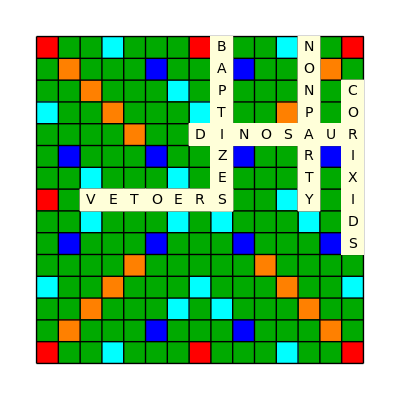

```mathematica
x=CreateInitialScrabbleBoard[];
Show[x,Epilog->epilogState]
```

```mathematica
Dataset[assoc]
```

### Check

```mathematica
Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]==Sort@Characters["SALTPANEXURBIAMWALMUSSORROED"]
```

True

### Finding Words when Necessary

```mathematica
dict=RandomSample[Import["CSW21.txt","List"]];
wordsByLength=GroupBy[dict,StringLength];
```

```mathematica
RandomChoice[wordsByLength[8]]
```

NOCTURIA

```mathematica
Select[wordsByLength[8],First[Characters[#]]=="C" && Last[Characters[#]]=="R"&&ContainsAll[Characters[#],{"A"}]&]
```

{CAREERER,CHAMPIER,CRAMPIER,CRAYONER,CLAQUEUR,CONTRAIR,CAVORTER,CHAFFIER,CHOKIDAR,CLAVIGER,CHATTIER,CLEANSER,CLANKIER,CHASSEUR,CATNAPER,COPASTOR,CATCHIER,CAROLLER,COLLATOR,CAPTURER,CELLARER,CREAMIER,COCHLEAR,COLINEAR,CYTASTER,CYMBALER,COPLANAR,CARESSER,CADASTER,CHARLIER,CHAUNTER,COFACTOR,CHAVVIER,COACHIER,CINGULAR,CAMELEER,CROSSBAR,COAUTHOR,CAROUSER,CHARRIER,CALENDAR,COENAMOR,CALLOWER,CAVILLER,CHAUFFER,CLASSIER,CREAKIER,CAPABLER,CROAKIER,CRABBIER,CANCELER,CAVEATOR,CABOCEER,CALLIPER,CRAVENER,CYCLECAR,COLANDER,COLEADER,CARMAKER,CRAYTHUR,CHICANER,CHANDLER,CAPSULAR,CRAPPIER,COMBATER,CALYPTER,COOLIBAR,CANEPHOR,CATHETER,CALCSPAR,CLARTIER,CANASTER,CHALKIER,CONSULAR,CHURIDAR,CHAPPIER,CREMATOR,CALCULAR,CRAWLIER,CYBERWAR,CUTWATER,CANALLER,CATAPHOR,CINNABAR,CATBRIAR,CREASIER,COMPARER,CAPSOMER,CLAMMIER,CAPMAKER,CRAFTIER,CISLUNAR,CELLULAR,CABALLER,CAIRNIER,CANVASER,CRAGGIER,CAVEOLAR,CALENDER,CRUSADER,COTTAGER,CHAPITER,CEDARIER,CRACKIER,CANNULAR,CRANKIER,COLUMNAR,CAPONIER,CLAMORER,CATBRIER,CAVALIER,CANDIDER,CANISTER,CAREENER,CIRCULAR,CHASMIER,CHELATOR,CULTIVAR,CONDYLAR,CLANGOUR,COAPPEAR,CLAGGIER,COANCHOR,CHANCIER}

### Array

```mathematica
addBlock[row_,col_,length_,dir_,grid_]:=Module[{newGrid=grid},
  If[dir=="Right",
    newGrid[[row,col;;col+length-1]]=GrayLevel[0]];
  If[dir=="Down",
    newGrid[[row;;row+length-1,col]]=GrayLevel[0]];
  newGrid
]
```

```mathematica
grid=ConstantArray["",{15,15}];
count=0;

grid=addBlock[8,2,7,"Right",grid];
turns[1]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[1,3,7,"Down",grid];
turns[2]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[1,5,7,"Down",grid];
turns[3]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[1,8,7,"Down",grid];
turns[4]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[1,7,8,"Right",grid];
turns[5]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[3,7,8,"Right",grid];
turns[6]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[5,7,8,"Right",grid];
turns[7]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[5,10,8,"Down",grid];
turns[8]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[10,8,8,"Right",grid];
turns[9]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[8,13,8,"Down",grid];
turns[10]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[8,15,8,"Down",grid];
turns[11]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[8,2,8,"Down",grid];
turns[12]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[8,4,8,"Down",grid];
turns[13]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}];
count++;

grid=addBlock[14,4,8,"Right",grid];
turns[14]=Grid[grid,
     Dividers->All,
     Spacings->{2,1}]
count++;
```

|  | GrayLevel[0] |  | GrayLevel[0] |  | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | 
 |  | GrayLevel[0] |  | GrayLevel[0] |  |  | GrayLevel[0] |  |  |  |  |  |  | 
 |  | GrayLevel[0] |  | GrayLevel[0] |  | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | 
 |  | GrayLevel[0] |  | GrayLevel[0] |  |  | GrayLevel[0] |  |  |  |  |  |  | 
 |  | GrayLevel[0] |  | GrayLevel[0] |  | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | 
 |  | GrayLevel[0] |  | GrayLevel[0] |  |  | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  | 
 |  | GrayLevel[0] |  | GrayLevel[0] |  |  | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  | 
 | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] |  | GrayLevel[0] |  |  | GrayLevel[0] |  | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  |  | GrayLevel[0] |  |  | GrayLevel[0] |  | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] |  |  |  | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  |  | GrayLevel[0] |  |  | GrayLevel[0] |  | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  |  | GrayLevel[0] |  |  | GrayLevel[0] |  | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  |  |  |  |  | GrayLevel[0] |  | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] | GrayLevel[0] |  | GrayLevel[0] |  | GrayLevel[0]
 | GrayLevel[0] |  | GrayLevel[0] |  |  |  |  |  |  |  |  | GrayLevel[0] |  | GrayLevel[0]

```mathematica
Animate[turns[i],{i,1,14,1}]
```

```mathematica
count
```

14

```mathematica
Counts[Flatten@grid]
```

<|→127,GrayLevel[0]→98|>